InterpolatingFunction::dmval: Input value {0.780684} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-22.9386} lies outside the range of data in the interpolating function. Extrapolation will be used.

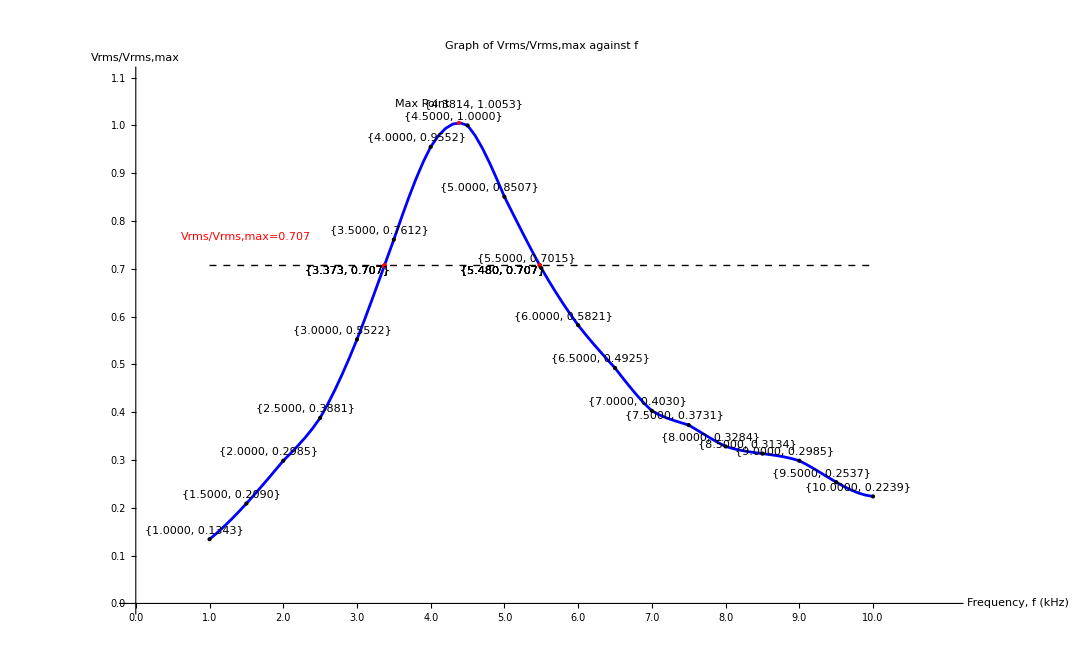

```mathematica
data={{1.0,0.1343},{1.5,0.2090},{2.0,0.2985},{2.5,0.3881},{3.0,0.5522},{3.5,0.7612},{4.0,0.9552},{4.5,1.0000},{5.0,0.8507},{5.5,0.7015},{6.0,0.5821},{6.5,0.4925},{7.0,0.4030},{7.5,0.3731},{8.0,0.3284},{8.5,0.3134},{9.0,0.2985},{9.5,0.2537},{10.0,0.2239}};

smoothCurve=Interpolation[data];

(*Find the maximum point on the smooth curve*)
maxPoint={x,smoothCurve[x]}/. FindMaximum[smoothCurve[x],{x,4.50}][[2]];

intersectionPoints={x,0.707}/. Table[FindRoot[smoothCurve[x]==0.707,{x,xi}],{xi,1,10,1}];

ListLinePlot[{Table[{x,smoothCurve[x]},{x,1,10,0.1}]},PlotStyle->Blue,AxesLabel->{"Frequency, f (kHz)","Vrms/Vrms,max"},PlotLabel->"Graph of Vrms/Vrms,max against f",Epilog->{Dashed,Line[{{1,0.707},{10,0.707}}],Red,PointSize[Medium],Point[intersectionPoints],Text[Style[ToString@NumberForm[#,{4,3}],Black],#+{-0.5,-0.01}]&/@intersectionPoints,Text["Vrms/Vrms,max=0.707",{1.5,0.707+0.06}],Text[Style[ToString@NumberForm[#,{4,4}],Black],#+{-0.2,0.02}]&/@data,Text[Style["Max Point",Black],maxPoint+{-0.5,0.04}],Red,PointSize[Medium],Point[{maxPoint}],Text[Style[ToString@NumberForm[maxPoint,{5,4}],Black],maxPoint+{0.2,0.04}],Black,PointSize[Medium],Point[data]},PlotRange->{{0,11.0},{0,1.1}},Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,10.5,0.5],{#,NumberForm[#,{3,1}]}&/@Range[0,1.1,0.1]}]
```